```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pbialas/Dydaktyka/2015_16/3DGraphicsProgrammingTutorials/Canvas2d

```mathematica
l=120
w=20
width=400
height=200
```

120

20

400

200

```mathematica
wagon={EdgeForm[Black],FaceForm[RGBColor[1, 0, 0]],Line[{{-w/2,w/2},{l+w/2,w/2}}],EdgeForm[Red],Rectangle[{0,0},{l,w}]}
```

{EdgeForm[GrayLevel[0]],FaceForm[RGBColor[1, 0, 0]],Line[{{-10,10},{130,10}}],EdgeForm[RGBColor[1, 0, 0]],Rectangle[{0,0},{120,20}]}

```mathematica
Graphics[
{FaceForm[], EdgeForm[Black],Rectangle[{0,0},{width,height}],
wagon
}//Scale[#,{1,-1}]&
]
```

-Graphics-

```mathematica
Clear[do]
```

```mathematica
compose[f_,g_]:=f[g[#]]&
```

```mathematica
rotate[angle_]:=Rotate[#,angle,{0,0}]&
```

```mathematica
translate[v_]:=Translate[#,v]&
```

```mathematica
flip[]:=Scale[#,{1,-1},{0,0}]&
```

```mathematica
do[ops_,currentTransform_, rest_]:=Module[{op},
If[ Length[ops]==0, Return[currentTransform]];
op=First[ops];
If[TrueQ[Head[op]==draw] ,Return[{currentTransform,First[op],Rest[ops]}],
Return[do[Rest[ops],compose[currentTransform,op],Rest[ops]]
]
]
]
```

```mathematica
x=do[{rotate[0],draw[wagon]},Identity,{}]
```

{Identity[(#1&)[#1]]&,{EdgeForm[GrayLevel[0]],FaceForm[RGBColor[1, 0, 0]],Line[{{-10,10},{130,10}}],EdgeForm[RGBColor[1, 0, 0]],Rectangle[{0,0},{120,20}]},{}}

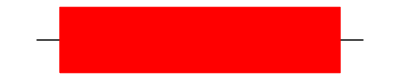

```mathematica
x[[1]][x[[2]] ]//Graphics
```

```mathematica
do[{f,draw[c]},Identity,{}]
```

{Identity[f[#1]]&,c,{}}

```mathematica
do[ops_]:=Module[{currentTransform=Identity,transform, acc={}, rest=ops, op,t},
While[Length[rest]≠0,
{transform, op,rest}=do[rest,currentTransform,rest];

AppendTo[acc,transform[op]];
currentTransform=transform;

];
acc
]
```

```mathematica
do[{flip[],rotate[30 Degree],draw[wagon]}]//Graphics
```

-Graphics-

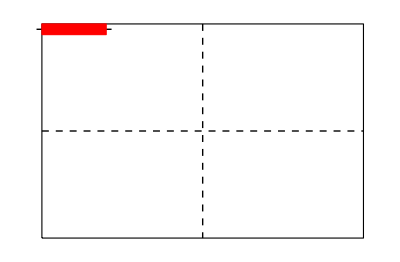

```mathematica
t0=Show[Graphics[{FaceForm[White],EdgeForm[Black],Rectangle[{0,0},{600,-400}],Dashed, Line[{{300,0},{300,-400}}],  Line[{{0,-200},{600,-200}}]}],do[{flip[],draw[wagon]}]//Graphics]
```

```mathematica
Export["t0.png", t0, ImageSize->{1024}]
```

t0.png

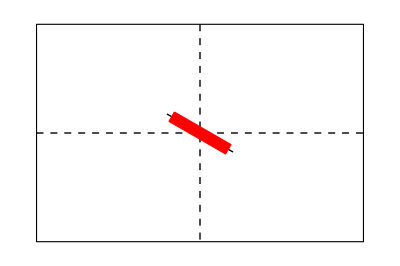

```mathematica
t1=Show[Graphics[{FaceForm[White],EdgeForm[Black],Rectangle[{0,0},{600,-400}],Dashed, Line[{{300,0},{300,-400}}],  Line[{{0,-200},{600,-200}}]}],do[{flip[],translate[{300,200}],rotate[Pi/6],translate[{-l/2,-w/2}],draw[wagon]}]//Graphics]
```

```mathematica
Export["t1.png", t1, ImageSize->{1024}]
```

t1.png

```mathematica
"t1.png"
```

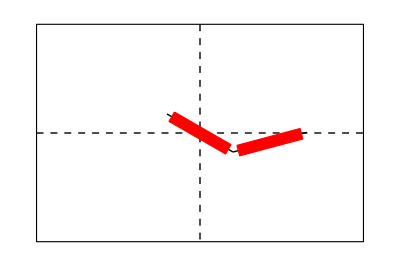

```mathematica
t2=Show[Graphics[{FaceForm[White],EdgeForm[Black],Rectangle[{0,0},{600,-400}],Dashed, Line[{{300,0},{300,-400}}],  Line[{{0,-200},{600,-200}}]}],do[{flip[],translate[{300,200}],rotate[Pi/6],translate[{-l/2,-w/2}],draw[wagon],translate[{l+w/2,w/2}],rotate[-Pi/4],translate[{w/2,-w/2}],draw[wagon]}]//Graphics]
```

```mathematica
Export["t2.png", t2, ImageSize->{1024}]
```

t2.png

```mathematica
set
```